```mathematica
Needs["Benchmarking`"]
```

```mathematica
BenchmarkReport[]
```

4hga6_shm50FrontEndObject[LinkObject["4hga6_shm", 3, 1]]50WolframMark Report

## CPUUUUUuUUUUUUuuuwuwuuuuwuuuww

If paralleldo is much faster than do or almost the same, take paralleldo : do = 7 : 3
Cuz for my understanding, one benifits much more for multi core, and one benifits much more for high frequency per core, no? 

if parado slower than do, take only do

```mathematica
TestSet:=(FindPI=Timer[N[π,10000000];];
SinglePrimee[a_]:=Do[If[PrimeQ[q]==True,1,0],{q,0,a}];
ParaPrime[a_]:=ParallelDo[If[PrimeQ[q]==True,1,0],{q,0,a}];
SinFindPrime=Timer[SinglePrimee[10^7.5];];
ParaFindPrime=Timer[ParaPrime[10^7.5];];
newtonIteration=Compile[{{z,_Complex},{n,_Integer}},Module[{zn=z},Do[zn=(2zn+1/zn^2)/3,{n}];
If[Re[zn]>0,1,If[Im[zn]>0,2,3]]],RuntimeAttributes->{Listable},Parallelization->True];
CompileTIme=Timer[ArrayPlot[Table[newtonIteration[x+I*y,25],{y,-5,5,2./199},{x,-5,5,2./199}]]];

EigenTimePara=Module[{a,b,m},Timer[SeedRandom[1];a=RandomReal[{},{1500,1500}];b=DiagonalMatrix[RandomReal[{},{1500}]];m=a.b.Inverse[a];ParallelDo[Eigenvalues[m],{10}]]];
EigenTimeSing=Module[{a,b,m},Timer[SeedRandom[1];a=RandomReal[{},{1500,1500}];b=DiagonalMatrix[RandomReal[{},{1500}]];m=a.b.Inverse[a];Do[Eigenvalues[m],{10}]]];
LinearSysSing=Module[{m,v},Timer[SeedRandom[1];m=RandomReal[{},{5000,5000}];v=RandomReal[{},{5000}];Do[LinearSolve[m,v],{10}]]];
LinearSysPara=Module[{m,v},Timer[SeedRandom[1];m=RandomReal[{},{5000,5000}];v=RandomReal[{},{5000}];ParallelDo[LinearSolve[m,v],{10}]]];
TransposeTime=Module[{m},Timer[SeedRandom[1];m=RandomReal[{},{8000,8000}];Do[Transpose[m],{10}]]];
RandomsortPara=Module[{a},Timer[SeedRandom[1];a=RandomInteger[{1,10^10},{3*10^6}];ParallelDo[Sort[a],{10}]]];
RandomsortSing=Module[{a},Timer[SeedRandom[1];a=RandomInteger[{1,10^10},{3*10^6}];Do[Sort[a],{10}]]];
Render3Dtime=RepeatedTiming[SphericalPlot3D[1+Sin[5 ϕ] Sin[10 θ]/10,{θ,0,2π},{ϕ,0,4π},ColorFunction->(ColorData["Rainbow"][#6]&),Mesh->None,PlotPoints->200,Boxed->False,Axes->False];][[1]];
NSloveTimePara=RepeatedTiming[Parallelize[NSolve[Sin[z+Sin[z+Sin[z]]]==Cos[z+Cos[z+Cos[z]]]&&-2<Re[z]<2&&-2<Im[z]<2,z];]];
NSloveTimeSingle=RepeatedTiming[NSolve[Sin[z+Sin[z+Sin[z]]]==Cos[z+Cos[z+Cos[z]]]&&-2<Re[z]<2&&-2<Im[z]<2,z];];

)
```

```mathematica
ParallelEvaluate
```

```mathematica
ParallelMap
```

```mathematica
TestSet
```

```mathematica
CPUScore:=Score[FindPI]+(3*Score[SinFindPrime]+7*Score[ParaFindPrime])/10+Score[CompileTIme]+(3*Score[EigenTimeSing]+7*Score[EigenTimePara])/10+(LinearSysPara+LinearSysSing)/2+Score[TransposeTime]+(7*Score[RandomsortPara]+3*Score[RandomsortSing])/10+1.5*Score[Render3Dtime]+(7*Score[NSloveTimePara[[1]]]+3*Score[NSloveTimeSingle[[1]]])/10
```

```mathematica
Score[t_]:=-900*ArcTan[0.035*t]+900;
CPUScore
```

6078.35

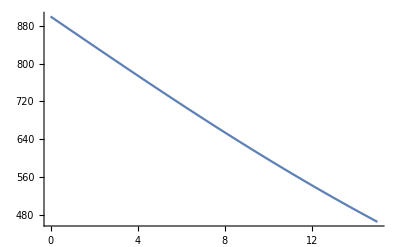

```mathematica
Plot[-900*ArcTan[0.035x]+900,{x,0,15},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
CPU:=(CloseKernels[];LaunchKernels[6];
SetAttributes[Timer,{HoldAll}];
Timer[expr_] :=
Block[
{result},
ClearSystemCache[];
result = AbsoluteTiming[expr];
  Return[result[[1]]]
];
TestSet;
CPUScore
)
```

```mathematica
CPU
```

6517.2

```mathematica
CloseKernels[];
LaunchKernels[6]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

```mathematica
SetAttributes[Timer,{HoldAll}];
Timer[expr_] :=
Block[
{result},
ClearSystemCache[];
result = AbsoluteTiming[expr];
  Return[result[[1]]]
]
```

```mathematica
FindPI=Timer[N[π,10000000];]
```

4.32124

```mathematica
SinglePrimee[a_]:=Do[If[PrimeQ[q]==True,1,0],{q,0,a}];
```

```mathematica
ParaPrime[a_]:=ParallelDo[If[PrimeQ[q]==True,1,0],{q,0,a}];
```

```mathematica
SinFindPrime=Timer[SinglePrimee[10^7.5];]
```

21.9599

```mathematica
ParaFindPrime=Timer[ParaPrime[10^7.5];]
```

3.84645

```mathematica
(*what's the percentage of parallel function in Mathhematica? *)
```

```mathematica
newtonIteration=Compile[{{z,_Complex},{n,_Integer}},Module[{zn=z},Do[zn=(2zn+1/zn^2)/3,{n}];
If[Re[zn]>0,1,If[Im[zn]>0,2,3]]],RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
CompileTIme=Timer[ArrayPlot[Table[newtonIteration[x+I*y,25],{y,-5,5,2./199},{x,-5,5,2./199}]]]
```

4.90032

```mathematica
EigenTimePara=Module[{a,b,m},Timer[SeedRandom[1];a=RandomReal[{},{1500,1500}];b=DiagonalMatrix[RandomReal[{},{1500}]];m=a.b.Inverse[a];ParallelDo[Eigenvalues[m],{10}]]]
```

7.55197

```mathematica
EigenTimeSing=Module[{a,b,m},Timer[SeedRandom[1];a=RandomReal[{},{1500,1500}];b=DiagonalMatrix[RandomReal[{},{1500}]];m=a.b.Inverse[a];Do[Eigenvalues[m],{10}]]]
```

9.62016

```mathematica
LinearSysSing=Module[{m,v},Timer[SeedRandom[1];m=RandomReal[{},{5000,5000}];v=RandomReal[{},{5000}];Do[LinearSolve[m,v],{10}]]]
```

7.63992

```mathematica
LinearSysPara=Module[{m,v},Timer[SeedRandom[1];m=RandomReal[{},{5000,5000}];v=RandomReal[{},{5000}];ParallelDo[LinearSolve[m,v],{10}]]]
```

8.79459

```mathematica
TransposeTime=Module[{m},Timer[SeedRandom[1];m=RandomReal[{},{8000,8000}];Do[Transpose[m],{10}]]]
```

3.72768

```mathematica
RandomsortPara=Module[{a},Timer[SeedRandom[1];a=RandomInteger[{1,10^10},{3*10^6}];ParallelDo[Sort[a],{10}]]]
```

1.82161

```mathematica
RandomsortSing=Module[{a},Timer[SeedRandom[1];a=RandomInteger[{1,10^10},{3*10^6}];Do[Sort[a],{10}]]]
```

4.73785

```mathematica
(*Need one for NDSlove (or find root if doesn't work out), but I couln't think of any long differential equation that takes time to solve*)

(*Is the 3D plot render by CPU or GPU?*)

(*I got 7 tests for GPU so far, just meed one for NDSlove and maybe one for rendering, don't need too many tests cuz the result is kinda consistant for performance*)

(*want to do a loading bar for benchmark*)

(*I am not showing the actual time to load each test, instead, just a score in the end *)


(*all tests should be around 3 ~ 10 ish second on my machine , so usually the whole test run for CPU will take around 1 ~ 3 min depends on the different laptop, a bit longer than the current benchmark, but it's normal and I think will be more accurate*)
```

```mathematica
Render3Dtime=RepeatedTiming[SphericalPlot3D[1+Sin[5 ϕ] Sin[10 θ]/10,{θ,0,2π},{ϕ,0,4π},ColorFunction->(ColorData["Rainbow"][#6]&),Mesh->None,PlotPoints->200,Boxed->False,Axes->False];][[1]]
```

7.444

```mathematica
NSloveTimePara=RepeatedTiming[Parallelize[NSolve[Sin[z+Sin[z+Sin[z]]]==Cos[z+Cos[z+Cos[z]]]&&-2<Re[z]<2&&-2<Im[z]<2,z];]]
```

{4.55,Null}

```mathematica
NSloveTimeSingle=RepeatedTiming[NSolve[Sin[z+Sin[z+Sin[z]]]==Cos[z+Cos[z+Cos[z]]]&&-2<Re[z]<2&&-2<Im[z]<2,z];]
```

{4.6,Null}

## RAMMMMMMAMMAMMMAMAMM

```mathematica
RAMSpeedScore:=(
Speed=D[Fit[{{RepeatedTiming[AA=ConstantArray[0.,{2000,2000}]][[1]],ByteCount[AA]},{RepeatedTiming[A=ConstantArray[0.,{5000,5000}]][[1]],ByteCount[A]},
{RepeatedTiming[B=ConstantArray[0.,{10000,10000}]][[1]],ByteCount[B]},{RepeatedTiming[CC=ConstantArray[0.,{15000,15000}]][[1]],ByteCount[CC]}},{1,x},x],x];ClearAll[A,B,CC,AA];Return[Time/(10^7)])
```

```mathematica
RAMSpeedScore
```

200.

```mathematica
RAMMuch:=300*Sqrt[SystemInformation["Machine","PhysicalTotal"][[1]]]
```

1196.27

```mathematica
RAMScore:=RAMMuch+RAMSpeedScore
```

```mathematica
RAMScore
```

1438.55

## DiskKKKKKKKKKKKK

```mathematica
DiskSpeed:=(Str=StringJoin[ConstantArray["0",100000000]];testfile =CreateFile[];
Diskwritetime=AbsoluteTiming[WriteString[testfile,Str]][[1]];
Diskreadtime=RepeatedTiming[ReadString[testfile]][[1]];
Diskwritespeed=ByteCount[Str]/Diskwritetime;
Diskreadspeed=ByteCount[Str]/Diskreadtime;
ClearAll[testfile];
)
```

```mathematica
DiskSpeed
```

```mathematica
Diskreadspeed
```

6.02×10^8

```mathematica
Diskwritespeed
```

3.22673×10^7

```mathematica
PacletInformation["Benchmarking"]
```

{Name→Benchmarking,Version→1.0.1,BuildNumber→,Qualifier→,WolframVersion→9+,SystemID→All,ProductName→All,Description→,Category→,Creator→,Publisher→,Support→,Internal→False,Updating→Manual,Location→C:\Users\dali7\AppData\Roaming\Mathematica\Paclets\Repository\Benchmarking-1.0.1,Context→{Benchmarking`},Enabled→True,Loading→Manual}

```mathematica
SystemOpen["C:\\Users\\dali7\\AppData\\Roaming\\Mathematica\\Paclets\\Repository\\Benchmarking-1.0.1"]
```

```mathematica
FileByteCount
```

```mathematica
Integers
```

```mathematica
str=StringJoin[ConstantArray["0",10000]];
```

```mathematica
ByteCount[str]
```

10248

```mathematica
file =CreateFile[]
```

C:\Users\dali7\AppData\Local\Temp\m-95c6aaba-9e73-4547-b8c8-2df68538c8c0

```mathematica
WriteString[file,str]//RepeatedTiming
```

{0.029,Null}

```mathematica
Quantity[10248/0.0032604, "Bytes"/"Seconds"]
```

3.14317×10^6 B/s

```mathematica
str=StringJoin[ConstantArray["e",1000000]];
```

```mathematica
ByteCount[str]
```

1000072

```mathematica
file3 =CreateFile[]
```

C:\Users\dali7\AppData\Local\Temp\m-31b95def-015e-47a2-9722-0b3b89ac7558

```mathematica
WriteString[file3,str];//AbsoluteTiming
```

{0.207669,Null}

```mathematica
WriteString[file3,str];//RepeatedTiming
```

{0.03,Null}

```mathematica
file2 =CreateFile[]
```

C:\Users\dali7\AppData\Local\Temp\m-83c3098b-ff0e-4b7e-9e31-be7b683c5630

```mathematica
WriteString[file2,str]//AbsoluteTiming
```

{0.0291395,Null}

```mathematica
Quantity[ByteCount[str]/0.0291395, "Bytes"/"Seconds"]
```

351688. B/s

```mathematica
str=ReadString[file2];//RepeatedTiming
```

{0.0035,Null}

```mathematica
Quantity[ByteCount[str]/0.0069143, "Bytes"/"Seconds"]
```

2.89266×10^8 B/s

```mathematica
BinaryReadList[file2];//RepeatedTiming
```

{0.047,Null}

## GPUUU~~